# DFML_DemonstrationResults

August H. Young (Frechette)

This file contains the overall result that should be generated by the user.

Edited: November 18 2022

The objective of this simulation is to show students that the “true” loss model is more accurate than the analytical model. We can show this by using the data we just generated.

Start by extracting our data

```mathematica
u1 = Table[Data[[i,7]],{i,2,Length[Data],1}];
u2 =Table[Data[[i,12]],{i,2,Length[Data],1}];
p1=Table[Data[[i,10]],{i,2,Length[Data],1}];
p2=Table[Data[[i,15]],{i,2,Length[Data],1}];
W1 = Data[[2,2]];W2 = Data[[2,3]];
```

Define the fluid parameters and flow conditions

```mathematica
μ = 1.0005*10^-3;(*kg m^-1s^-1*)
ρ = 9.99*10^2;(*kg m^-3*)
U1 = Table[Data[[i,4]],{i,2,Length[Data],1}];
RE = ρ*U1*W1/μ;
```

Generate our loss coefficients

K_(L,approx)=(1-A_1/A_2)^2

K_(L,true)=  1-(v_2/v_1)^2+(p_1-p_2)/(1/2 ρ v_1^2)

```mathematica
KlApprox=(1-W1/W2)^2;
KlTrue= 1-(u2/u1)^2+(p1-p2)/(1/2 ρ u1^2);
```

```mathematica
KlTrue
```

{0.0527226,0.0264978,0.0177029,0.0132914,0.0106383}

Plot the results

```mathematica
DataApprox = Transpose[{RE,Table[KlApprox,{i,Length[KlTrue]}]}];
DataTrue = Transpose[{RE,KlTrue}];

ListPlot[{DataApprox,DataTrue},PlotLabels->{"Approximate","True"},AxesLabel->{"RE"},PlotLabel->"Loss Coefficient v RE"]
```

-Graphics-

Explore Further

Generate the corresponding pressure drop

```mathematica
dPApprox= KlApprox ρ U1^2; PDataApprox = Transpose[{RE,dPApprox}];
dPTrue= KlTrue ρ u1^2; PDataTrue= Transpose[{RE,dPTrue}];
dP = p2 - p1;PData= Transpose[{RE,dP}];
```

Plot the results

```mathematica
ListPlot[{PDataApprox,PDataTrue,PData},PlotLabels->{"Approximate","True","Numerical"},AxesLabel->{"RE"},PlotLabel->"Pressure Loss v RE"]
```

-Graphics-

Extrapolate

→ Let’s fit our results to see what each model does throughout the entire laminar regime.

```mathematica
yP=NonlinearModelFit[PData,a x^2+b x,{a,b},x];
yTrue=NonlinearModelFit[PDataTrue,a x^2+b x,{a,b},x];
yApprox=NonlinearModelFit[PDataApprox,a x^2+b x,{a,b},x];
```

Our results suggest, to a good degree of fit

```mathematica
{yP["RSquared"],yTrue["RSquared"],yApprox["RSquared"]}
```

{0.997625,0.999999,1.}

That the approximate analytical model behaves well for low Reynolds numbers:

```mathematica
Plot[{yApprox[x],yTrue[x],yP[x]},{x,0,200},PlotLabels->{"Approximate","True","Numerical"},AxesLabel->{"RE"},PlotLabel->"Pressure Drop v RE"]
```

-Graphics-

But does not for the entire laminar flow regime:

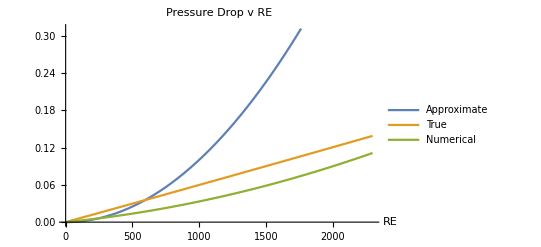

```mathematica
Plot[{yApprox[x],yTrue[x],yP[x]},{x,0,2300},PlotLegends->{"Approximate","True","Numerical"},AxesLabel->{"RE"},PlotLabel->"Pressure Drop v RE"]
```

```mathematica
Plot[{Abs[(yApprox[x]-yP[x])/yP[x]]*100,Abs[(yTrue[x]-yP[x])/yP[x]]*100},{x,0,2300},PlotLabels->{"Approximate Pressure Drop Error","True Pressure Drop Error"},PlotRange->All,PlotLabel->"Percent Error in Pressure Drop Approximations",AxesLabel->{"RE"},Filling->Bottom]
```

-Graphics-